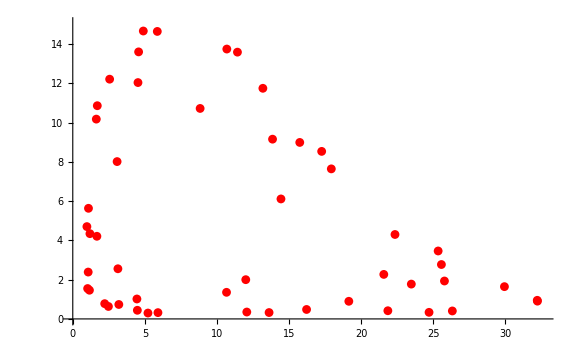

```mathematica
parasitosis[a_,rho_,capacity_,eggCount_,N0_,P0_,T_]:=(
host=Table[0,T];
parasitoid=Table[0,T];

host[[1]]=N0;
parasitoid[[1]]=P0;

For[k=1,k<T,k++,
host[[k+1]]= Exp[-a*parasitoid[[k]]+rho*(1-host[[k]]/capacity)]*host[[k]];
parasitoid[[k+1]]=eggCount*(1-Exp[-a*parasitoid[[k]]])*host[[k]];
];

{host,parasitoid}
)

(* Steady cycle
sol=parasitosis[0.22,1.6,21.5,1,5,2,400];
*)
(* Random
sol=parasitosis[0.21,2.65,25,1,12,2,1000];
*)

(* Inner pseudocycloid cycle
sol=parasitosis[0.222, 2.05, 25, 1, 12, 2, 1000];
*)

(* Ghost
sol=parasitosis[0.2, 2.05, 22.5, 1, 14, 2, 1000];
*)
sol=parasitosis[0.222, 2.05, 25, 1, 12, 2, 1000];

(* Vortex
sol=parasitosis[0.222,2.05,14,1,11,1.6,700];
*)

parasitoidAnim=Animate[
ListPlot[{{sol[[1]][[j]],sol[[2]][[j]]}}, 
PlotStyle->Red,ImageSize->Large,PlotRange->{{0,Max[sol[[1]]]},{0,Max[sol[[2]]]}}]
,{j,1,T,1},AnimationRunning->False,DefaultDuration->120,DisplayAllSteps->True
]

parasitoidPic=ListPlot[Table[{sol[[1]][[j]],sol[[2]][[j]]},{j,1,T}], PlotStyle->Red,PlotRange->{{0,Max[sol[[1]]]},{0,Max[sol[[2]]]}},ImageSize->Large]
(*
(*Slow and garbage*)
ListAnimate[
Table[ListPlot[{{sol[[1]][[j]],sol[[2]][[j]]}}, 
PlotStyle->Red,ImageSize->Large,PlotRange->{{0,Max[sol[[1]]]},{0,Max[sol[[2]]]}}]
,{j,1,T,1}],AnimationRunning->False,AnimationRate->3
]
*)
```